```mathematica
ClearAll["Global`*"]
w=2/3;
period=2*Pi/w;
A=1.5;
tmax=1000;
soln=ParametricNDSolve[{theta''[t]+(1/Q) * theta'[t]+Sin[theta[t]]==A  Cos[w t],theta[0]==0,theta'[0]==0},theta,{t,0,tmax},{Q}];
```

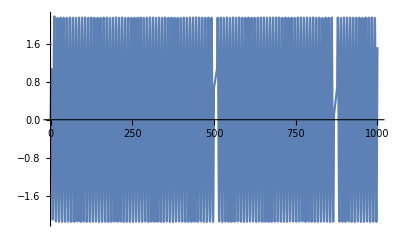

```mathematica
Q=1;
Plot[theta[Q][x]/.soln,{x,0,tmax}]
```

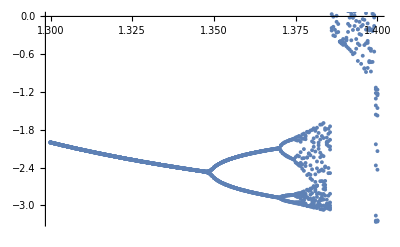

```mathematica
tdel=period;
Qmin=1.3;
Qmax=1.4;
numPoints=200;
Qres=numPoints/(Qmax-Qmin);
start=tdel*90;
end=tdel*100;
length=Length[Table[x,{x,start,end,tdel}]];
bifur=Flatten[Table[Transpose[{
ConstantArray[i,length],Flatten[Table[theta[i][x]/.soln,{x,start,end,tdel}]]}],
{i,Qmin,Qmax,1/Qres}],1];
ListPlot[bifur]
```